```mathematica
V= 10
h1=1
h2=10
h3 = 0.1
```

10

1

10

0.1

```mathematica
t11=0.09638891129126581
t21=0.0999584008892277
t31=0.05573634242004828
t12=0.07338506354797933
t22=0.07498243792213373
t32=0.046639605310341184
t13=0.24695460532448796
t23=0.2988911265824967
t33=0.10421434313901705
```

0.0963889

0.0999584

0.0557363

0.0733851

0.0749824

0.0466396

0.246955

0.298891

0.104214

```mathematica
rce1 = {x'[t]==V*Cos[β[t]]-(V/h1)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h1)(Cos[β[t]])^2}
rce2 = {x'[t]==V*Cos[β[t]]-(V/h2)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h2)(Cos[β[t]])^2}
rce3 = {x'[t]==V*Cos[β[t]]-(V/h3)y[t],y'[t]==V*Sin[β[t]],β'[t]==(V/h3)(Cos[β[t]])^2}
```

{x'[t]==10 Cos[β[t]]-10 y[t],y'[t]==10 Sin[β[t]],β'[t]==10 Cos[β[t]]^2}

{x'[t]==10 Cos[β[t]]-y[t],y'[t]==10 Sin[β[t]],β'[t]==Cos[β[t]]^2}

{x'[t]==10 Cos[β[t]]-100. y[t],y'[t]==10 Sin[β[t]],β'[t]==100. Cos[β[t]]^2}

```mathematica
sol11 = NDSolve[Join[rce1,{x[0]==1,y[0]==0,β[0]==2.6924934515066306}],{x,y,β},{t,0,3600}]
sol21 = NDSolve[Join[rce2,{x[0]==1,y[0]==0,β[0]==3.0916550055755416}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol31  = NDSolve[Join[rce3,{x[0]==1,y[0]==0,β[0]==1.9153177950415883}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol12 =NDSolve[Join[rce1,{x[0]==0.75,y[0]==0,β[0]==2.7899198806413206}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol22 = NDSolve[Join[rce2,{x[0]==0.75,y[0]==0,β[0]==3.1041189856089515}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol32 = NDSolve[Join[rce3,{x[0]==0.75,y[0]==0,β[0]==33.39182471068394}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

```mathematica
sol13= NDSolve[Join[rce1,{x[0]==3,y[0]==0,β[0]==2.251523898983622}],{x,y,β},{t,0,3600}]
sol23= NDSolve[Join[rce2,{x[0]==3,y[0]==0,β[0]==2.993244986423751}],{x,y,β},{t,0,3600}]
sol33= NDSolve[Join[rce3,{x[0]==3,y[0]==0,β[0]==1.7604031632713453}],{x,y,β},{t,0,3600}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],β→InterpolatingFunction[…]}}

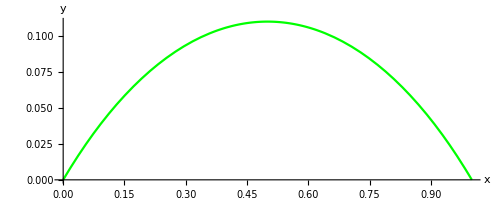

```mathematica
graf11  =ParametricPlot[Table[{x[t],y[t]}/.sol11],{t,0,t11},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Green}]
```

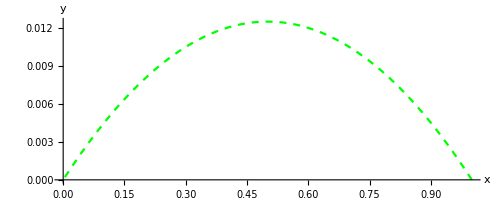

```mathematica
graf21  =ParametricPlot[Table[{x[t],y[t]}/.sol21],{t,0,t21},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Green,Dashed}]
```

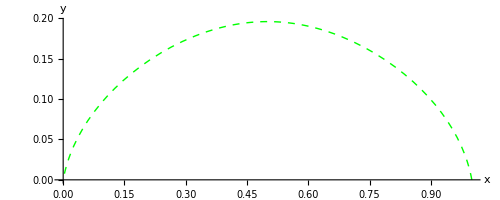

```mathematica
graf31  =ParametricPlot[Table[{x[t],y[t]}/.sol31],{t,0,t31},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Green,Thick,Dashed}]
```

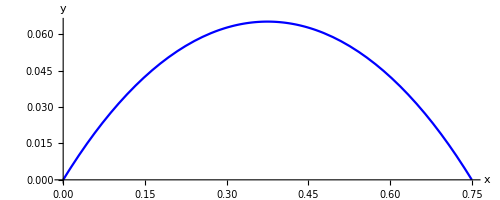

```mathematica
graf12  =ParametricPlot[Table[{x[t],y[t]}/.sol12],{t,0,t12},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Blue}]
```

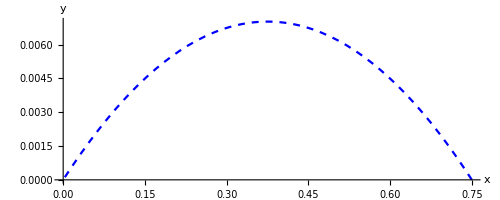

```mathematica
graf22  =ParametricPlot[Table[{x[t],y[t]}/.sol22],{t,0,t22},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Blue,Dashed}]
```

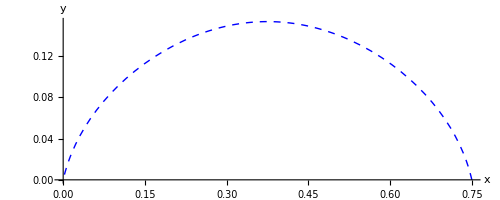

```mathematica
graf32  =ParametricPlot[Table[{x[t],y[t]}/.sol32],{t,0,t32},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Blue,Dashed,Thick}]
```

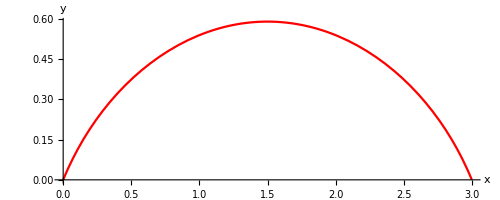

```mathematica
graf13  =ParametricPlot[Table[{x[t],y[t]}/.sol13],{t,0,t13},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Red}]
```

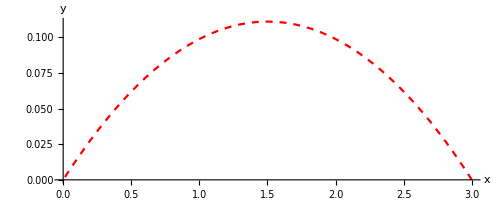

```mathematica
graf23  =ParametricPlot[Table[{x[t],y[t]}/.sol23],{t,0,t23},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Red,Dashed}]
```

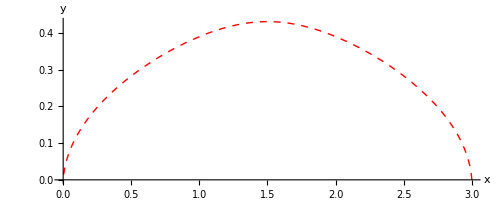

```mathematica
graf33  =ParametricPlot[Table[{x[t],y[t]}/.sol33],{t,0,t33},AxesLabel->{x,y},PlotRange->All,PlotStyle->{Red,Dashed,Thick}]
```

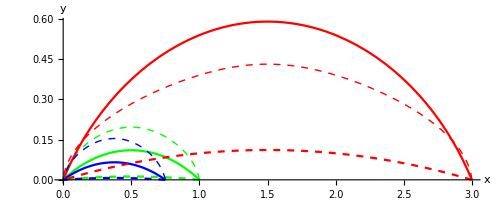

```mathematica
Show[graf11,graf21,graf31,graf12,graf13,graf22,graf23,graf32,graf33]
```

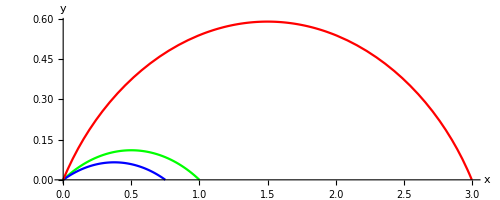

```mathematica
Show[graf11,graf12,graf13]
```

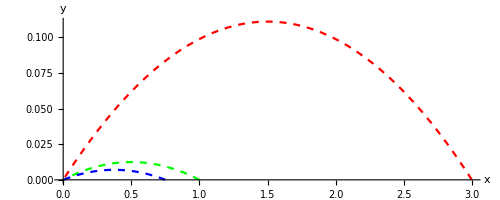

```mathematica
Show[graf21,graf22,graf23]
```

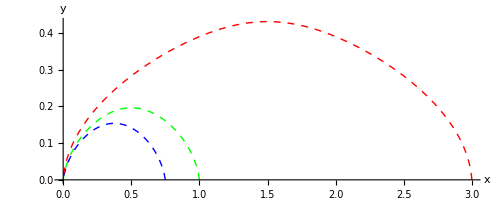

```mathematica
Show[graf31,graf32,graf33]
```

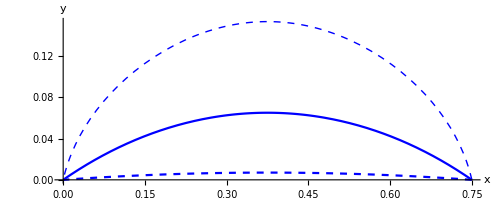

```mathematica
Show[graf12,graf22,graf32]
```

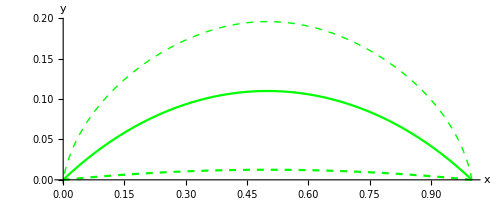

```mathematica
Show[graf11,graf21,graf31]
```

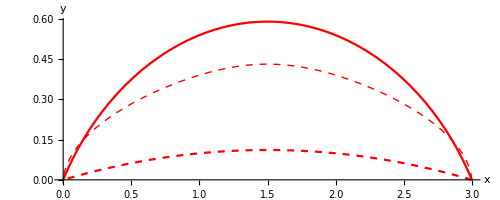

```mathematica
Show[graf13,graf23,graf33]
```

```mathematica
Tabulka0 = Table[{{1,0},{5,0},{-5,0}}]
```

{{1,0},{5,0},{-5,0}}

```mathematica
{{1,0},{0.75,0},{3,0}}
```

{{1,0},{0.75,0},{3,0}}

```mathematica
Tabulka1 = Table[{t11,t12,t13}]
```

{0.0963889,0.0733851,0.246955}

```mathematica
Tabulka2 = Table[{t21,t22,t23}]
```

{0.0999584,0.0749824,0.298891}

```mathematica
Tabulka3 = Table[{t31,t32,t33}]
```

{0.0557363,0.0466396,0.104214}

```mathematica
NumberForm[Grid[{{"Start X/Y","h = 1","h = 10","h = 0.1"},{TableForm[Tabulka0],TableForm[Tabulka1],TableForm[Tabulka2],TableForm[Tabulka3]}},Frame->All],7]
```

Start X/Y | h = 1 | h = 10 | h = 0.1
1 | 0
5 | 0
-5 | 0 | 0.09638891
0.07338506
0.2469546 | 0.0999584
0.07498244
0.2988911 | 0.05573634
0.04663961
0.1042143

```mathematica
Tabulka11=Table[{β[0]/.sol11,β[0]/.sol12,β[0]/.sol13}]
```

{{2.69249},{2.78992},{2.25152}}

```mathematica
Tabulka22=Table[{β[0]/.sol21,β[0]/.sol22,β[0]/.sol23}]
```

{{3.09166},{3.10412},{2.99324}}

```mathematica
Tabulka33=Table[{β[0]/.sol31,β[0]/.sol32,β[0]/.sol33}]
```

{{1.91532},{33.3918},{1.7604}}

```mathematica
NumberForm[Grid[{{"Start X/Y","h = 1","h = 10","h = 0.1"},{TableForm[Tabulka0],TableForm[Tabulka11],TableForm[Tabulka22],TableForm[Tabulka33]}},Frame->All],7]
```

Start X/Y | h = 1 | h = 10 | h = 0.1
1 | 0
5 | 0
-5 | 0 | 2.692493
2.78992
2.251524 | 3.091655
3.104119
2.993245 | 1.915318
33.39182
1.760403

```mathematica
'
```